```mathematica
SetDirectory[NotebookDirectory[]];
```

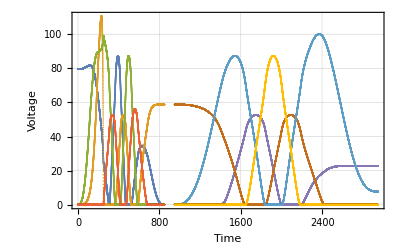

```mathematica
th=100;
TT1=850;
part1={"part1table1.csv",
"part1table2.csv",
"part1table3.csv",
"part1table4.csv"};
part2={"part2table1.csv",
"part2table2.csv",
"part2table3.csv",
"part2table4.csv"};
data1=Table[Transpose[Import[part1[[i]],"Table"]][[1]],{i,1,Length[part1]}];
data2=Table[Transpose[Import[part2[[i]],"Table"]][[1]],{i,1,Length[part2]}];
points1=Table [Table[{(j-1)/10,data1[[i]][[j]]},{j,1,Length[data1[[1]]]}],{i,1,Length[data1]}];
points2=Table[Table[{(j-1)/10+th+TT1,data2[[i]][[j]]},{j,1,Length[data2[[1]]]}],{i,1,Length[data2]}];
ListPlot[Join[points1,points2],Frame->True,GridLines->Automatic,FrameLabel->{"Time","Voltage"},PlotRange->All]
```

```mathematica
(*blue is 1*)
(*purple is 2*)
(*yellow is 3*)
(*green is 4*)
```

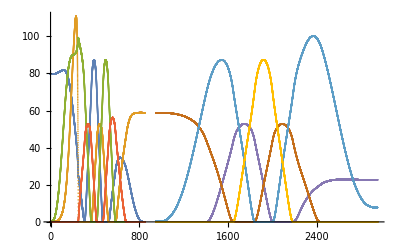

```mathematica
linearLength=35;
SMPclk=12500;
BPW=34;
part1start=points1⟦1,1,1⟧;
part1end=points1⟦1,Length[data1⟦1⟧],1⟧;
part2start=points2⟦1,1,1⟧;
part2end=points2⟦1,Length[data2⟦1⟧],1⟧;
f=Table[Interpolation[points1⟦i⟧],{i,1,Length[part1]}];
g=Table[Interpolation[points2⟦i⟧],{i,1,Length[part2]}];
highrespoints1=Table[Table[{j,Abs[f⟦i⟧[j]]},{j,part1start,part1end,(BPW*linearLength)/SMPclk}],{i,1,Length[part1]}];
highrespoints2=Table[Table[{j,Abs[g⟦i⟧[j]]},{j,part2start,part2end,(BPW*linearLength)/SMPclk}],{i,1,Length[part2]}];
ListPlot[Join[highrespoints1,highrespoints2]]
```

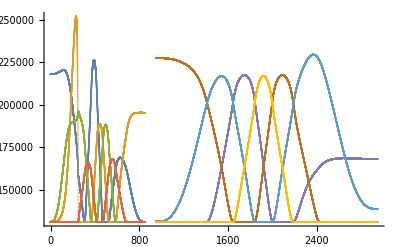

```mathematica
numpsu={2,2,2,2};
maxcurrent={60,60,100,100};
highrespoints1=Table[Table[{j,Round[(Abs[f⟦i⟧[j]]/(numpsu⟦i⟧*maxcurrent⟦i⟧)5+5)/10 2^18]},{j,part1start,part1end,(BPW*linearLength)/SMPclk}],{i,1,Length[part1]}];
numpsu={2,2,2,2};
maxcurrent={60,60,100,100}/1.5;
highrespoints2=Table[Table[{j,Round[(Abs[g⟦i⟧[j]]/(numpsu⟦i⟧*maxcurrent⟦i⟧)5+5)/10 2^18]},{j,part2start,part2end,(BPW*linearLength)/SMPclk}],{i,1,Length[part2]}];
ListPlot[Join[highrespoints1,highrespoints2]]
```

```mathematica
Dimensions[highrespoints1⟦3⟧]
```

{8929,2}

```mathematica
highrespoints1⟦1,1000;;2000⟧//TableForm;
```

```mathematica
For[ii=1,ii≤4,ii++,
filename=ToString["part1table"<>ToString[ii]<>"HR_12.5MHz.bin"];
BinaryWrite[filename,Transpose[highrespoints1⟦ii⟧]⟦2⟧,"UnsignedInteger32"];
Close[filename];
]
For[ii=1,ii≤4,ii++,
filename=ToString["part2table"<>ToString[ii]<>"HR_12.5MHz.bin"];
BinaryWrite[filename,Transpose[highrespoints2⟦ii⟧]⟦2⟧,"UnsignedInteger32"];
Close[filename];
]
```

```mathematica
Export["part1table1HR.txt",Transpose[highrespoints1[[1]]][[2]],"Table"]
Export["part1table2HR.txt",Transpose[highrespoints1[[2]]][[2]],"Table"]
Export["part1table3HR.txt",Transpose[highrespoints1[[3]]][[2]],"Table"]
Export["part1table4HR.txt",Transpose[highrespoints1[[4]]][[2]],"Table"]
Export["part2table1HR.txt",Transpose[highrespoints2[[1]]][[2]],"Table"]
Export["part2table2HR.txt",Transpose[highrespoints2[[2]]][[2]],"Table"]
Export["part2table3HR.txt",Transpose[highrespoints2[[3]]][[2]],"Table"]
Export["part2table4HR.txt",Transpose[highrespoints2[[4]]][[2]],"Table"]
```

part1table1HR.txt

part1table2HR.txt

part1table3HR.txt

part1table4HR.txt

part2table1HR.txt

part2table2HR.txt

part2table3HR.txt

part2table4HR.txt

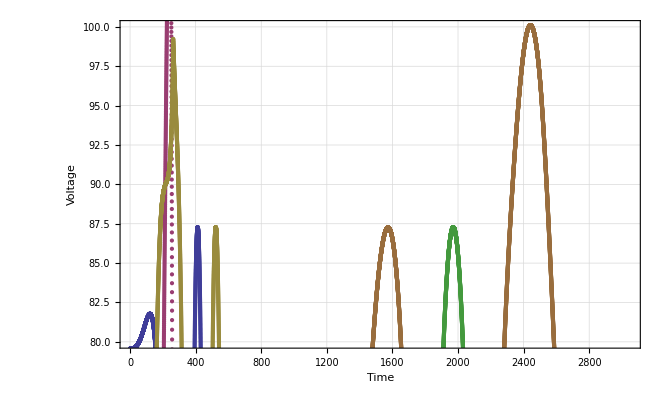

```mathematica
th=100;
TT1=850;
part1={"part1table1HR.txt",
"part1table2HR.txt",
"part1table3HR.txt",
"part1table4HR.txt"};
part2={"part2table1HR.txt",
"part2table2HR.txt",
"part2table3HR.txt",
"part2table4HR.txt"};
data1=Table[Transpose[Import[part1[[i]],"Table"]][[1]],{i,1,Length[part1]}];
data2=Table[Transpose[Import[part2[[i]],"Table"]][[1]],{i,1,Length[part2]}];
points1=Table [Table[{(j-1)/10,data1[[i]][[j]]},{j,1,Length[data1[[1]]]}],{i,1,Length[data1]}];
points2=Table[Table[{(j-1)/10+th+TT1,data2[[i]][[j]]},{j,1,Length[data2[[1]]]}],{i,1,Length[data2]}];
ListPlot[Join[points1,points2],Frame->True,GridLines->Automatic,FrameLabel->{"Time","Voltage"},PlotRange->{80,100}]
```

```mathematica
data1=Transpose[Import["part2table1HR.txt","Table"]];
Length[Transpose[data1]]
```

21009

```mathematica
data1[[1]][[5000;;5001]]
```

{0.550427,0.556245}

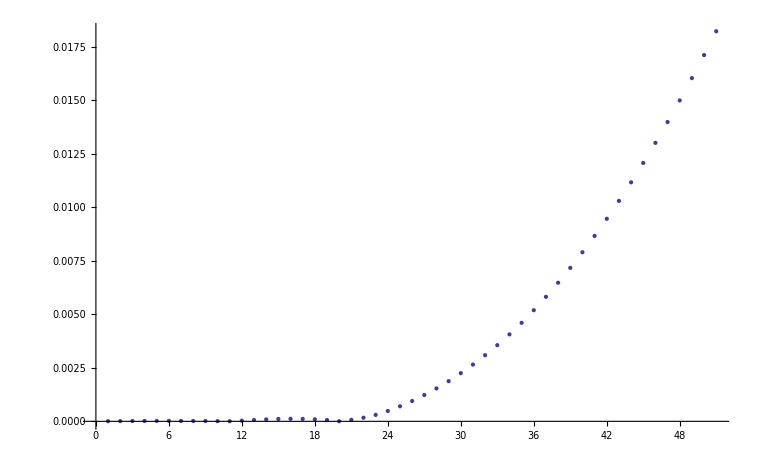

```mathematica
ListPlot[data1[[1]][[4800;;4850]]]
```

```mathematica
data1[[1]]
```

{0.156895,0.156895,0.156895,0.156895,0.156895,0.156895,0.156895,0.156895,0.156895,0.156894,0.156894,0.156894,0.156894,0.156894,0.156894,0.156893,0.156893,0.156893,0.156893,0.156892,0.156892,0.156891,0.156891,«20963»,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381,22.6381}